# PeterBurbery/CombinatoricsPaclet

Combinatorics functions for subsets, tuples, and permutations

## Paclet Manifest

"Documentation"

"English"

"Guides"

"CombinatorialFunctions.nb"DocumentationEnglishGuidesCombinatorialFunctions.nb

"TuplesPermutationsAndSubsets.nb"DocumentationEnglishGuidesTuplesPermutationsAndSubsets.nb

"ReferencePages"

"Symbols"

"DiscreteInverseEqual.nb"DocumentationEnglishReferencePagesSymbolsDiscreteInverseEqual.nb

"DiscreteInverseLessThan.nb"DocumentationEnglishReferencePagesSymbolsDiscreteInverseLessThan.nb

"EnumerateMultisetPartialDerangements.nb"DocumentationEnglishReferencePagesSymbolsEnumerateMultisetPartialDerangements.nb

"LehmerCodeFromPermutation.nb"DocumentationEnglishReferencePagesSymbolsLehmerCodeFromPermutation.nb

"MultisetPartialDerangements.nb"DocumentationEnglishReferencePagesSymbolsMultisetPartialDerangements.nb

"NDigitNumbers.nb"DocumentationEnglishReferencePagesSymbolsNDigitNumbers.nb

"OrderedTupleFromIndex.nb"DocumentationEnglishReferencePagesSymbolsOrderedTupleFromIndex.nb

"OrderedTupleIndex.nb"DocumentationEnglishReferencePagesSymbolsOrderedTupleIndex.nb

"OriginalReferencePages"

"MultisetPartialDerangements.nb"DocumentationEnglishReferencePagesSymbolsOriginalReferencePagesMultisetPartialDerangements.nb

"PartialDerangements.nb"DocumentationEnglishReferencePagesSymbolsOriginalReferencePagesPartialDerangements.nb

"PartialDerangements.nb"DocumentationEnglishReferencePagesSymbolsPartialDerangements.nb

"PermutationFromIndex.nb"DocumentationEnglishReferencePagesSymbolsPermutationFromIndex.nb

"PermutationIndex.nb"DocumentationEnglishReferencePagesSymbolsPermutationIndex.nb

"PermutationToTableaux.nb"DocumentationEnglishReferencePagesSymbolsPermutationToTableaux.nb

"RepetendCycleLength.nb"DocumentationEnglishReferencePagesSymbolsRepetendCycleLength.nb

"SubsetFromIndex.nb"DocumentationEnglishReferencePagesSymbolsSubsetFromIndex.nb

"SubsetIndex.nb"DocumentationEnglishReferencePagesSymbolsSubsetIndex.nb

"TableauxToPermutation.nb"DocumentationEnglishReferencePagesSymbolsTableauxToPermutation.nb

"TupleFromIndex.nb"DocumentationEnglishReferencePagesSymbolsTupleFromIndex.nb

"TupleIndex.nb"DocumentationEnglishReferencePagesSymbolsTupleIndex.nb

"Tutorials"

"Kernel"

"CombinatoricsPaclet copy.wl"KernelCombinatoricsPaclet copy.wl

"CombinatoricsPaclet.wl"KernelCombinatoricsPaclet.wl

"EnumerateMultisetPartialDerangements.wl"KernelEnumerateMultisetPartialDerangements.wl

"LehmerCodeFromIndex.wl"KernelLehmerCodeFromIndex.wl

"Multichoose.wl"KernelMultichoose.wl

"MultisetPartialDerangements.wl"KernelMultisetPartialDerangements.wl

"PartialDerangements.wl"KernelPartialDerangements.wl

"PermutationFromIndex.wl"KernelPermutationFromIndex.wl

"PermutationFromLehmerCode.wl"KernelPermutationFromLehmerCode.wl

"LICENSE"LICENSE

"PacletInfo.wl"PacletInfo.wl

"ResourceDefinition.nb"ResourceDefinition.nb

## Web Content

### Headline Image

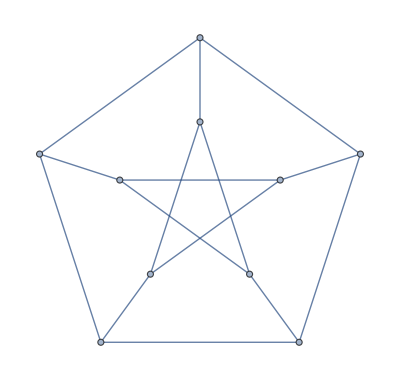

### Basic Description

This paclet is for Project Euler problems and other applications of combinatorics.

### Details

I would like to give credit to Ed Pegg Jr who developed many of the functions that make up this paclet. Many of the functions are available from the Resource Function Repository.

### Primary Context

MyPublisherID`MyPaclet`

### Main Guide Page

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad[];
```

```mathematica
Needs[];
```

### Basic Examples

Find the millionth permutation with 10 items:

```mathematica
PermutationFromIndex[10^6,10]
```

{3,8,9,4,10,2,6,5,7,1}

To solve the challenge Lexicographic permutations at Project Euler, subtract 1 and join the digits with FromDigits:

```mathematica
FromDigits[PermutationFromIndex[10^6,10]-1]
```

2783915460

The googolth 111-tuple:

```mathematica
TupleFromIndex[10^100,111]
```

{4,4,4,4,6,5,4,7,1,0,3,1,1,1,2,6,2,6,6,6,6,3,1,3,1,4,7,3,6,3,1,3,2,3,0,6,1,2,6,6,3,7,4,1,1,5,6,2,1,1,2,1,4,5,1,6,3,5,0,2,3,2,6,0,7,2,5,6,3,2,0,3,2,2,3,1,3,7,1,5,2,0,5,7,6,4,0,0,0,1,2,5,1,1,2,3,1,7,6,1,6,5,6,1,6,0,2,1,1,2,6}

Find some binomial representations for the number 403:

```mathematica
Column[Row[Riffle[Table[TraditionalForm[Binomial[(ToString/@#)[[n]],ToString[n]]],{n,1,Length[#]}],"+"]]&/@Table[SubsetFromIndex[403+1,n],{n,2,7}],Alignment->Center]
```

Binomial[25, 1]+Binomial[28, 2]
Binomial[3, 1]+Binomial[9, 2]+Binomial[14, 3]
Binomial[2, 1]+Binomial[6, 2]+Binomial[8, 3]+Binomial[11, 4]
Binomial[2, 1]+Binomial[3, 2]+Binomial[6, 3]+Binomial[9, 4]+Binomial[10, 5]
Binomial[2, 1]+Binomial[5, 2]+Binomial[6, 3]+Binomial[7, 4]+Binomial[9, 5]+Binomial[10, 6]
Binomial[2, 1]+Binomial[3, 2]+Binomial[4, 3]+Binomial[6, 4]+Binomial[7, 5]+Binomial[8, 6]+Binomial[11, 7]

Solve Project Euler's challenge Even Fibonacci numbers by finding even Fibonacci numbers not exceeding 4 million and summing:

```mathematica
Select[EvenQ[#]&][Fibonacci[Range[DiscreteInverseLessThan[Fibonacci[#],4 10^6]]]]
```

{2,8,34,144,610,2584,10946,46368,196418,832040,3524578}

```mathematica
Total[Select[EvenQ[#]&][Fibonacci[Range[DiscreteInverseLessThan[Fibonacci[#],4 10^6]]]]]
```

4613732

Find the first number whose Fibonacci number contains 1000 digits to solve Project Euler 1000-digit Fibonacci number:

```mathematica
DiscreteInverseEqual[IntegerLength[Fibonacci[#]],1000]
```

4782

Find the longest repetend cycle length up to but not including 1000 to solve Project Euler puzzle Reciprocal cycles:

```mathematica
First[Flatten[Position[RepetendCycleLength[Range[999]],Max[RepetendCycleLength[Range[999]]]]]]
```

983

### Scope

## Source & Additional Information

### Creator

Peter Cullen Burbery

### Source Control Repository

https://github.com/PeterCullenBurbery/combinatorics-paclet

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

permutations

subsets

tuples

combinatorics

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Original Source References and Attributions

Source, reference or citation

### Links

Link to other related material

### Compatibility

#### Wolfram Language Version

13.1+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

Wolfram Language system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

Wolfram Language built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

Paclet dependenciesDisclosuresPacletDependenciesChoose this option if your paclet directly installs or updates any additional paclets. Paclets that are included with the Wolfram system do not require a disclosure.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes

Additional information about limitations, issues, etc.